```mathematica
ClearAll["Global`*"]
```

```mathematica
vv:=7
K[n_] := If[ n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
K5[n_] := K[n](1-If[ Mod[n,vv]==0,n,0])
K6[n_] := K[n]-If[ Floor[Log[vv,n]]==Log[vv,n],n /Log[vv,n],0]
P[n_,0]=1; 
P[n_, k_] := P[n,k] = Sum[ K6[j]P[Floor[n/j],k-1],{j,2,n}]
En[n_] := En[n] = Sum[ 1/(k!) P[n,k],{k,0, Log[2,n]}]
En[n_,z_] := En[n] = Sum[ (z^k)/(k!) P[n,k],{k,0, Log[2,n]}]
en[n_] := En[n]-En[n-1]
LAdd[n_] := Sum[ vv^k/k,{k,1,Log[vv,n]}]
LAdd2[n_] := Sum[(-1)^k vv^k,{k,1,Log[vv,n]}]
PP[n_,k_] := PP[n,k]=Sum[ 1/k-PP[Floor[n/j],k+1],{j,2,n}]
```

```mathematica
P[100,1]+LAdd[100]
```

428/15

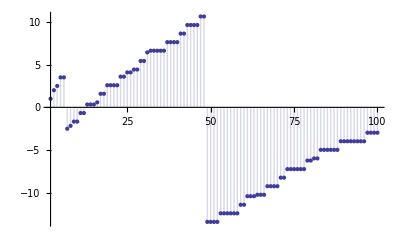

```mathematica
DiscretePlot[{P[n,1]},{n,2,100}]
```

```mathematica
Table[{n,en[n]},{n,2,50}]//TableForm
```

2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | -6
8 | 1
9 | 1
10 | 1
11 | 1
12 | 1
13 | 1
14 | -6
15 | 1
16 | 1
17 | 1
18 | 1
19 | 1
20 | 1
21 | -6
22 | 1
23 | 1
24 | 1
25 | 1
26 | 1
27 | 1
28 | -6
29 | 1
30 | 1
31 | 1
32 | 1
33 | 1
34 | 1
35 | -6
36 | 1
37 | 1
38 | 1
39 | 1
40 | 1
41 | 1
42 | -6
43 | 1
44 | 1
45 | 1
46 | 1
47 | 1
48 | 1
49 | -6
50 | 1

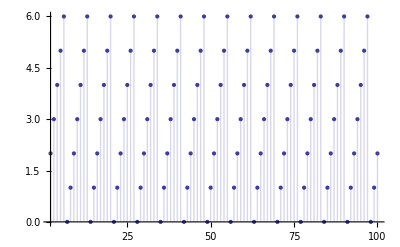

```mathematica
DiscretePlot[En[n],{n,2,100}]
```

```mathematica
Table[ {n, En[n], Mod[n,vv]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 2 | 2
3 | 3 | 3
4 | 4 | 4
5 | 5 | 5
6 | 6 | 6
7 | 14 | 0
8 | 15 | 1
9 | 16 | 2
10 | 17 | 3
11 | 18 | 4
12 | 19 | 5
13 | 20 | 6
14 | 28 | 0
15 | 29 | 1
16 | 30 | 2
17 | 31 | 3
18 | 32 | 4
19 | 33 | 5
20 | 34 | 6
21 | 42 | 0
22 | 43 | 1
23 | 44 | 2
24 | 45 | 3
25 | 46 | 4
26 | 47 | 5
27 | 48 | 6
28 | 56 | 0
29 | 57 | 1
30 | 58 | 2
31 | 59 | 3
32 | 60 | 4
33 | 61 | 5
34 | 62 | 6
35 | 70 | 0
36 | 71 | 1
37 | 72 | 2
38 | 73 | 3
39 | 74 | 4
40 | 75 | 5
41 | 76 | 6
42 | 84 | 0
43 | 85 | 1
44 | 86 | 2
45 | 87 | 3
46 | 88 | 4
47 | 89 | 5
48 | 90 | 6
49 | 147 | 0
50 | 148 | 1
51 | 149 | 2
52 | 150 | 3
53 | 151 | 4
54 | 152 | 5
55 | 153 | 6
56 | 161 | 0
57 | 162 | 1
58 | 163 | 2
59 | 164 | 3
60 | 165 | 4
61 | 166 | 5
62 | 167 | 6
63 | 175 | 0
64 | 176 | 1
65 | 177 | 2
66 | 178 | 3
67 | 179 | 4
68 | 180 | 5
69 | 181 | 6
70 | 189 | 0
71 | 190 | 1
72 | 191 | 2
73 | 192 | 3
74 | 193 | 4
75 | 194 | 5
76 | 195 | 6
77 | 203 | 0
78 | 204 | 1
79 | 205 | 2
80 | 206 | 3
81 | 207 | 4
82 | 208 | 5
83 | 209 | 6
84 | 217 | 0
85 | 218 | 1
86 | 219 | 2
87 | 220 | 3
88 | 221 | 4
89 | 222 | 5
90 | 223 | 6
91 | 231 | 0
92 | 232 | 1
93 | 233 | 2
94 | 234 | 3
95 | 235 | 4
96 | 236 | 5
97 | 237 | 6
98 | 294 | 0
99 | 295 | 1
100 | 296 | 2

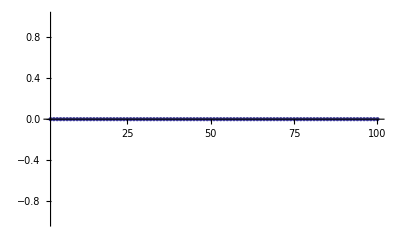

```mathematica
DiscretePlot[P[n,1]-PP[n,1]+LAdd[n],{n,2,100}]
```